# Meteorite landings

## Estevão Alves

```mathematica
{Entity["Word","meteorites"][EntityProperty["Word","Definitions"]], Entity["Word","landings"]["Definitions"][[3]]}
```

"meteorite", "Noun" -> "stony or metallic object that is the remains of a meteoroid that has reached the earth's surface",
 "landing", "Noun", "ComeToEarth" -> "the act of coming down to the earth (or other surface)".

Interest in the word meteorite over the  years:

```mathematica
WolframAlpha["Meteorite landings",IncludePods->"BookMatchFrequency:WordData",AppearanceElements->{"Pods"},TimeConstraint->{20,Automatic,Automatic,Automatic},PodStates->{"BookMatchFrequency:WordData__Log scale","BookMatchFrequency:WordData__Linear scale","BookMatchFrequency:WordData__Raw","BookMatchFrequency:WordData__Binned"}]
```

WolframAlphaQueryResults

## History

“In August, 1933, at the Field Museum of Natural History in Chicago, The Society for Research on Meteorites was founded [...]. Within five years, the Society had doubled in size, with members from the U.S.A.and ten other nations. Annual meetings were suspended during World War II (1942 through 1945) and when it reconvened in 1946 the members adopted the name' The Meteoritical Society'. [...]. Throughout the 1950 s the Society was widely regarded as a small, disorganized and essentially moribund organization.

Revitalization of the Society began in the 1960s after the advent of the Space Age when the Society steadily gained members with expertise in mineralogy, petrology, isotope geochemistry, electron microprobe and neutron activation analysis, and impact dynamics.”

- The Meteoritical Society [1]

## Introduction

Any kind of data can contain  a huge variety of implicit information. Using Wolfram Language (WL), one can extract and abstract different kinds of data. Here, the goal is to demonstrate how one can import data, from the Wolfram Data Repository (WDR) and/or from an external source, and reshape it as one needs. Every kind of data probably will have different forms of reshaping, however,  some functions may be the same. Here, one will be able to organize each information, filter, sort, plot and locate the information in a map. Even though we demonstrate a limited number of functions, one should know that the possibilities of reshaping and creating visualizations and endless using WL.

## Obtaining the data

In our case, one can find the meteorites landings in Wolfram Data Repository [2]. Using the data from WDR it is really easy and one can find at https://datarepository.wolframcloud.com/resources/Meteorite-Landings. 
To get the data from WDR, one just have to do:

```mathematica
ResourceData["Meteorite Landings"]
```

Dataset[<>]

and with that, one can simply do all kinds of visualisations, as a map, for example:

```mathematica
GeoGraphics[{Red,PointSize[0.01],Opacity[0.2],Point@DeleteMissing[ResourceData["Meteorite Landings"][All,"Coordinates"]]},GeoRange->"World",ImageSize->500]
```

-Graphics-

However, let’s say that one couldn’t find the right data at WDR or that the data there isn’t updated. In our case, I found a updated data at NASA [3]. So, let’s import it to this notebook.

```mathematica
meteoriteLandingImportedData =Dataset@Import["https://data.nasa.gov/resource/gh4g-9sfh.json?$limit=50000","RawJSON"]
```

Dataset[<>]

In this case, the number of rows (45,716) are the same as in WDR’s data. However, the imported data doesn’t have the same shape as the last one that we got from ResourceData. In the next sections, we will reshape this data and create some visualisations with it.

## Reshaping the imported data

To begin with our computation, let’s make the meteoriteLandingImportedData looks like the ResourceData that we got. We have to create an association with the keys’ names in capital,  remove the missing data,  transform the mass number to grams, format the datetime to year, and we need to create a single column to Coordinates using the GeoPosition function.

```mathematica
meteoritesReshapedData = meteoriteLandingImportedData[All, DeleteMissing[<| "Name" -> #name, "ID" -> #id,"NameType" -> #nametype,"Classification" -> #recclass,"Mass" -> Quantity[#["mass"],"Grams"],"Fall" -> #fall,"Year" -> DateObject[#["year"], DateFormat ->"Year"],"Coordinates" ->If[#["reclat"]=="0.000000"||#["reclong"]=="0.000000",Missing[],GeoPosition[ToExpression@{#["reclat"],#["reclong"]}]]|>, 1, Infinity] &]
```

Dataset[<>]

## Plots, filters and Maps

Now, our dataset is ready. We have the following columns to work with :

```mathematica
Keys[meteoritesReshapedData][1]//Normal
```

{Name,ID,NameType,Classification,Mass,Fall,Year,Coordinates}

We can start by getting the 5 most massive meteorites using Kilograms:

```mathematica
Quantity[Normal@Take[Sort[
 ToExpression[Normal@QuantityMagnitude[DeleteMissing[meteoritesReshapedData[[All,"Mass"]],1,1]]],Greater],5]/1000,"Kilograms"]
```

{60000 kg,58200 kg,50000 kg,30000 kg,28000 kg}

Now, we can also show how the data has increased by year. First, let’s see what happened when the Meteoritical Society stopped during the World War II (as mentioned in the introduction).

To begin with, lets sort the data by year

```mathematica
dataSortedByYear = Sort[meteoritesReshapedData,#1[["Year"]]< #2[["Year"]] &]
```

Dataset[<>]

We now can see the behavior of the data collection during the World War II. The amount of data was increasing  and then stopped in

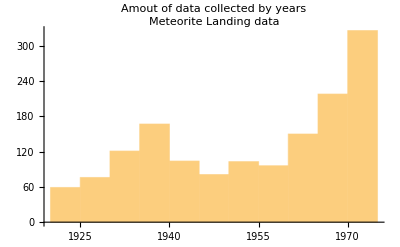

```mathematica
DateHistogram[dataSortedByYear[[All,"Year"]][[1000;;2500]],PlotLabel->"Amout of data collected by years",ChartLabels->Placed[{"Meteorite Landing data"},Above],LabelingFunction->(Row[#2]&)]
```

A different kind of approach it is to use the data in maps. Lets manipulate the map with the meteorite landings sorted by year,

```mathematica
Manipulate[GeoGraphics[{PointSize->0.01,Red,Opacity->0.3,
Point[Normal@DeleteMissing[dataSortedByYear[[All,"Coordinates"]],1,1][[;;x]]]},GeoRange->"World"] ,
Row[{
Control[{x,0,50000,1000,ControlType -> Manipulator, ImageMargins -> 5}]
}]
]
```

## Conclusion

We used the meteorite landings data but one can use any kind of that to do the same as we did here. The options to create a good presentation using Wolfram Language are endless. We could go from getting the data to a basic timeline map plot. Of course that there are a lot more that one can do using the same data but the purpose of this essay is completed.

## References

[1] Marvin, U. B.  The Meteoritical Society: 1933-1993,  Meteoritics, volume 28, number 3, page 261-314, July 1993;
[2]  Wolfram Research, “Meteorite Landings” from the Wolfram Data Repository (2017) https://doi.org/10.24097/wolfram.08737.data;
[3]  The Meteoritical Society, Meteorite Landings, NASA’s Open Data Portal. https://data.nasa.gov/Space-Science/Meteorite-Landings/gh4g-9sfh (Metadata last update: Jun/2018);